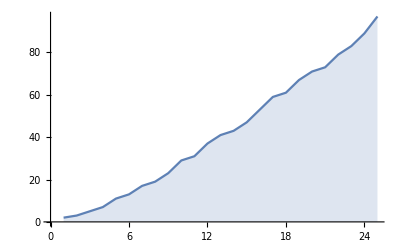

-Graphics3D-

```mathematica
ListLinePlot[Prime[Range[25]], Filling->Axis]
ListPlot3D[{{1,1,1,1},{1,2,1,2},{1,1,3,1},{1,2,1,4}}, Mesh->All] (*задаются высоты поверхности*)
```

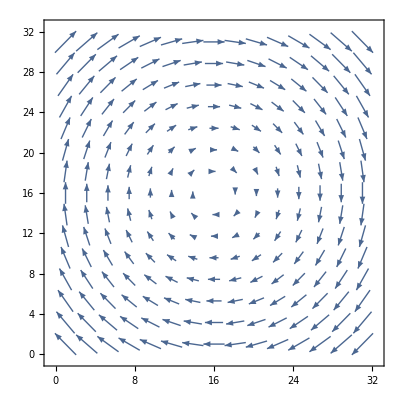

```mathematica
ListVectorPlot[Table[{y, -x}, {x, -3, 3, 0.2}, {y, -3,3, 0.2}]]
```

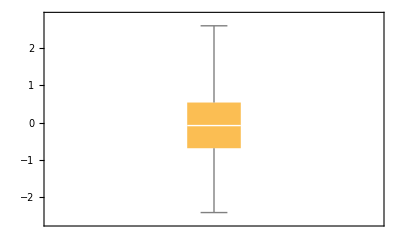

NormalDistribution[0,1]

```mathematica
BoxWhiskerChart[RandomVariate[NormalDistribution[0,1], 100]]
NormalDistribution[0,1](*значение 0 и отклонение 1*)
```

{Piecewise[{{0.3^k 0.7^(50-k) Binomial[50,k], 0≤k≤50}, {0, True}}],Piecewise[{{8.88178×10^-16 Binomial[50,k], 0≤k≤50}, {0, True}}],Piecewise[{{0.2^(50-k) 0.8^k Binomial[50,k], 0≤k≤50}, {0, True}}]}

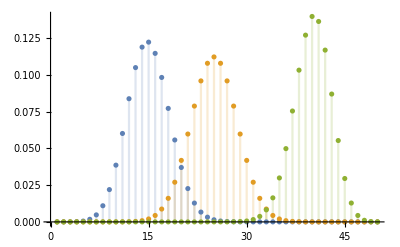

```mathematica
Table[PDF[BinomialDistribution[50,p], k], {p, {0.3, 0.5, 0.8}}]
(*50 испытаний и p - вероятность успеха*)
DiscretePlot[Evaluate[%], {k,1,50}]
```

```mathematica
ChromaticityPlot3D["sRGB"]
```

-Graphics3D-

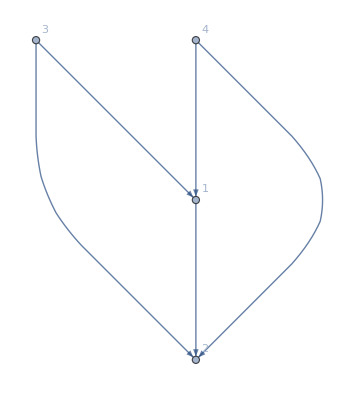

```mathematica
LayeredGraphPlot[{1->2, 3->1, 3-> 2, 4->1, 4->2}, VertexLabels->Automatic]
```

{1→2,1→3,2→4,2→5,3→6,3→7,4→8}

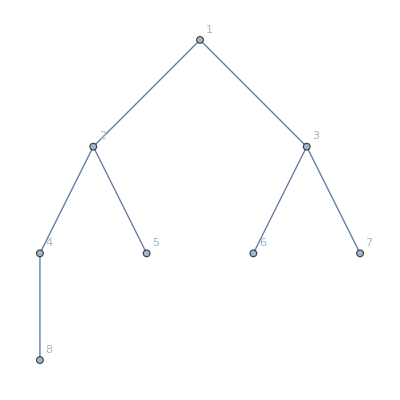

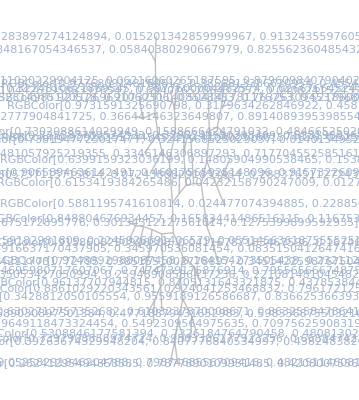

```mathematica
g={1->2, 1->3, 2-> 4,2-> 5, 3->6,3->7, 4->8}
TreePlot[g, VertexLabeling->True]

ClusteringTree[RandomColor[40], ClusterDissimilarityFunction->"Centroid", GraphLayout->"RadialEmbedding"]
```